## Orbital Elements From State Vector

```mathematica
(* Clear all the variables in the memory *)
ClearAll["Global`*"];
(*Quit[];*)
(* This section of code is Made to show a table of variables used in this problems ,it`s very useful in case dealing with neumerical problems *)
CreateWindow@PaletteNotebook[{Button["Refresh",vars=Framed[Grid[Select[With[{expr=ToExpression@#},
{#,Head[expr],Which[ListQ[expr],Dimensions[expr],NumericQ[expr],expr,StringQ[expr],StringLength[expr],True,"-"]}]&/@Names["Global`*"],
(#[[2]]=!=Symbol)&],Alignment->Left],FrameStyle->None,FrameMargins->5]],Dynamic[vars]},WindowElements->{"VerticalScrollBar"},WindowTitle->"Global`*"];
```

### Problem Definition

-Graphics-

### Solution

```mathematica
r={-6045,-3490,2500};
v={-3.457,6.618,2.533};
μ=398600;
(* output in thid form *)
(*[e,h,θ,Ω,ω,i]*)
output=StateVector2OrbitalElements[r,v,μ];
Framed[Style[TableForm[{{output[[1]]},{output[[2]]},{output[[3]]},{output[[4]]},{output[[5]]},
                       {output[[6]]}},TableHeadings->{{"e","h","θ","Ω","ω","i"}}],{Large,Red}]]
```

Part::partw: Part 4 of StateVector2OrbitalElements[{-6045,-3490,2500},{-3.457,6.618,2.533},398600] does not exist.

Part::partw: Part 5 of StateVector2OrbitalElements[{-6045,-3490,2500},{-3.457,6.618,2.533},398600] does not exist.

Part::partw: Part 6 of StateVector2OrbitalElements[{-6045,-3490,2500},{-3.457,6.618,2.533},398600] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

e | -6045
-3490
2500
h | -3.457
6.618
2.533
θ | 398600
Ω | StateVector2OrbitalElements[{-6045,-3490,2500},{-3.457,6.618,2.533},398600]⟦4⟧
ω | StateVector2OrbitalElements[{-6045,-3490,2500},{-3.457,6.618,2.533},398600]⟦5⟧
i | StateVector2OrbitalElements[{-6045,-3490,2500},{-3.457,6.618,2.533},398600]⟦6⟧

### Algorithm used

```mathematica
StateVector2OrbitalElements[r_,v_,μ_]:=Module[{rmod,vmod,vrmod,h,hmod,i,n,nmod,Ω,e,emod,ω,θ},
rmod=Norm[r]//N;
vmod=Norm[v]//N;
vrmod=(r.v)/rmod;
h=r×v;
hmod=Norm[h]//N;     (* First orbit element *)
i=ArcCos[h[[3]]/hmod]; (* 2nd orbit element *)
n={0,0,1}×h;
nmod=Norm[n]//N;
Ω=Piecewise[{{ArcCos[N[[1]]/nmod],n[[2]]≥0},{2 π-ArcCos[n[[1]]/nmod],n[[2]]<0}}];(* 3rd orbit element *)
e=1/μ*((vmod^2-μ/rmod)*r-rmod*vrmod*v);
emod=Norm[e];  (* 4th orbit element *)
ω=Piecewise[{{ArcCos[(n.e)/(nmod*emod)],e[[3]]≥0},{2 π-ArcCos[(n.e)/(nmod*emod)],e[[3]]<0}}];(* 5th orbit element *)
θ=Piecewise[{{ArcCos[(e.r)/(rmod*emod)],vrmod≥0},{2 π-ArcCos[(e.r)/(rmod*emod)],vrmod<0}}];(* 6th orbit element *)
Return[{emod,hmod,θ*180/π,Ω*180/π,ω*180/π,i*180/π}];
]
```

### Verification

-Graphics-
-Graphics-

#### Range Kutta Function Implementation

```mathematica
RK4[dy_,X0_,t0_,tf_,dt_]:=Module[{k1,k2,k3,k4,X,t,solution,i,j,n,dim},
dim=Dimensions[X0,1][[1]];                                                           (* dimension of matrix *) 
n=(tf-t0)/dt;                                                                                       (* Number of devisions in the given time interval *)
solution =Table[0,{j,1,n,1},{i,1,dim,1}];                 (* initialization of solution matrix *)
(* put initial values in sol*)
For[i=1,i≤ dim,i++,
solution[[1]][[i]]=X0[[i]];];
(* Initializing Value Of X*)
X=X0;
t=t0;
(* Core of the function *)
For[i=1,i≤n-1,i++,
(* we eill compute slope at start of region   1st correction *)
k1=dy[X,t];
(* second correction at middle of the region *)
k2=dy[X+dt k1/2,t+dt/2];
(* third correction at middle of the region *)
k3=dy[X+dt k2/2,t+dt/2];
(* fourth correction at end of the region *)
k4=dy[X+dt k3,t+dt];
t=t+dt;
X=X+(k1 +2 k2 +2 k3 +k4)dt/6;

(*Assign solution at this point to solution matrix*)
For[j=1,j≤dim,j++,
solution[[i+1]][[j]]=X[[j]];];
];
Return[solution];
]
```

#### Problem Definition

```mathematica
me=5.974*10^24;                     (*Mass of the earth*)
Rearth=6378;                        (* Radius of the Earth*)
ms=1000;                            (*Mass of satellite*)
G=6.67259*10^-20;                   (*Universal Gravitational Constant*)
μ=G*(me+ms);                        (* Gravitational Parameter *)
t0=0;                               (*initial time*)
tf=4.5*60*60;                      (*final time of simulation *)
n=1000;
dt=(tf-t0)/n;                     (*time step *)
X0={{8000,0,6000},{0,7,0}};              (*Initial Condition *)
dy[X_,t_]:={X[[2]],(-μ X[[1]])/Norm[X[[1]]]^3};
map=-Graphics-;
```

#### Solving Our Problem

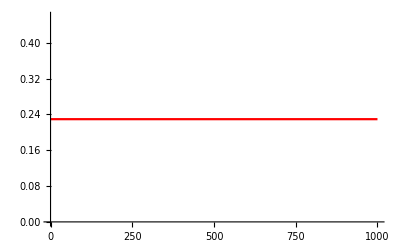
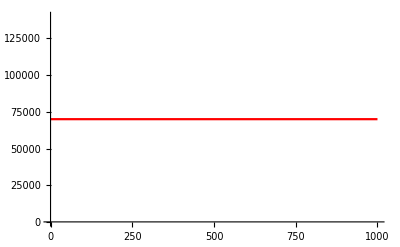
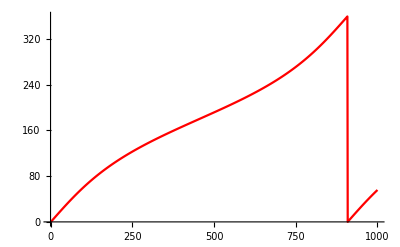
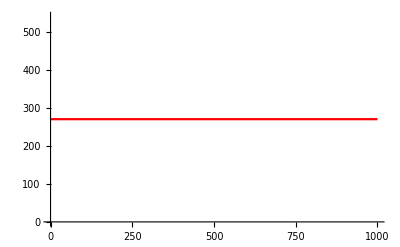
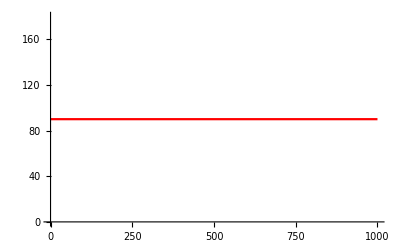
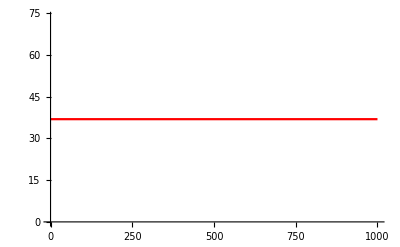
e | -Graphics-
h | -Graphics-
θ | -Graphics-
Ω | -Graphics-
ω | -Graphics-
i | -Graphics-

```mathematica
Sol=RK4[dy,X0,t0,tf,dt];  (* Recall RK4 to Get Solution *)
R1=Sol[[All,1]];          (* Position Vector of Earth due to Satellite Mass *)
V1=Sol[[All,2]];          (* Velocity Vector of Earth *)
solution =Table[0,{j,1,n,1},{i,1,6,1}]; 
For[i=1,i<=Length[R1],i++,
solution[[i]]=StateVector2OrbitalElements[R1[[i]],V1[[i]],μ];]
fig1=ListLinePlot[solution[[All,1]],PlotStyle->Red];
fig2=ListLinePlot[solution[[All,2]],PlotStyle->Red];
fig3=ListLinePlot[solution[[All,3]],PlotStyle->Red];
fig4=ListLinePlot[solution[[All,4]],PlotStyle->Red];
fig5=ListLinePlot[solution[[All,5]],PlotStyle->Red];
fig6=ListLinePlot[solution[[All,6]],PlotStyle->Red];
TableForm[{{fig1},{fig2},{fig3},{fig4},{fig5},{fig6}},TableHeadings->{{"e","h","θ","Ω","ω","i"}}]
```